```mathematica
(*ep=0.08;β=0.7;γ=0.8;δ=1;d1 =1; d2=0;*)
(*Change of variables from FHN2 -> FHN1*)
maxtime=100;
(*δ=1;d1 =1; d2=0;τ= 0.2;α=0.3; γt =0.1 ;(*Chen*)*)
(*δ=1;d1 =1; d2=0;τ= 20;α=0.3; γt =0.1 ;(*Modified Chen*)*)
δ=1;d1 =1; d2=0;τ= 1/0.015;α=0.045; γt =3.5 ;(*Argentina 10.1006/jtbi.2000.2044*)
If[(1-α)^2<4/γ,Print["Unique root"],Print["Multiple Roots"]]

A= Sqrt[1-α+α^2]/3;
B =3A^3;
K1=3A^2;
K2=Sqrt[3]A;
v0=-(1+α)/(3A);
γ=3A^2 γt;
β=γ(δ v0-v0^3/3)-v0;
ep=1/(9 τ A^4);
w0=(v0+β)/γ;

Print["\\gamma = ",γ,", \\quad \\beta = ",β, ", \\quad \\varepsilon = ", ep,", \\quad v_0 = ",v0,", \\quad w_0= ",w0,","]
Print["\\tau = ",τ,", \\quad \\alpha = ",α,", \\quad \\tilde{\\gamma} = ",γt,","]
Print["A= ",A,", \\quad B = ",B, ", \\quad K_1 = ",K1, ", \\quad K_2 = ",K2,","]
```

Unique root

\gamma = 1.11653, \quad \beta = 0.329164, \quad \varepsilon = 0.147397, \quad v_0 = -1.06821, \quad w_0= -0.661909,

\tau = 66.6667, \quad \alpha = 0.045, \quad \tilde{\gamma} = 3.5,

A= 0.326092, \quad B = 0.104026, \quad K_1 = 0.319008, \quad K_2 = 0.564808,

```mathematica
(*Plot[{v-v^3/3,(v+β)/γ},{v,-2,2},PlotRange->{-2,2}]
Plot[{x(1-x)(x-α),x/γt},{x,-2,2},PlotRange->{-2,2}]*)
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

{InterpolatingFunction[…],InterpolatingFunction[…]}

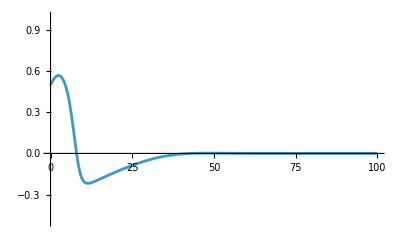

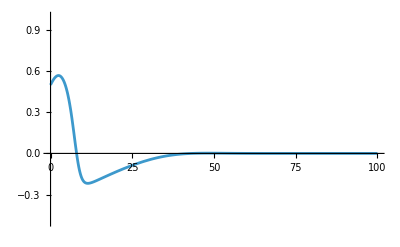

```mathematica
(*Comparison Simulation*)
{X1,Y1}=NDSolveValue[{x'[t]==x[t](1-x[t])(x[t]-α)-y[t],τ y'[t]==x[t]-γt y[t],x[0]==0+0.5,y[0]==0},{x,y},{t,0,maxtime}]
{V1,W1}=NDSolveValue[{v'[t]==δ v[t]-v[t]^3/3-w[t],w'[t]==ep(v[t]-γ w[t] + β),v[0]==X1[0]/A+v0,w[0]==Y1[0]/B+w0},{v,w},{t,0,maxtime*K1}]

Plot[A(V1[K1 s]-v0),{s,0,maxtime},PlotRange->{-0.5,1}]
Plot[X1[s],{s,0,maxtime},PlotRange->{-0.5,1}]
```